```mathematica
Heaviside[x_]:=Which[x<0,0,x==0,1,x>0,1]
Ef[t_,x_,S_]:=∑_(i=1)^Length[S] Heaviside[t-S[[i]]] ⅇ^(x S[[i]])
tr={30,60,90};
Ω[n_,β_,k_,t_]:=(β-k n +k Ef[t,ⅈ,tr])ⅇ^(-ⅈ t)+k(n-Ef[t,0,tr])
Ωc[n_,β_,k_,t_]:=(β-k n +k Ef[t,-ⅈ,tr])ⅇ^(ⅈ t)+k(n-Ef[t,0,tr])
A[n_,t_,tr_,k_]:={tr1=Join[tr,{t}];tr2=Join[{0},tr];tr3=tr2-tr1;dt=If[Min[tr]>t,t,Min[Pick[#,UnitStep@#,1]&@(t-tr)]];
iact=If[Min[tr]>t,0,Length[Pick[#,UnitStep@#,1]&@(t-tr)]];
Exp[ⅈ k^2(n-iact)^2(dt-Sin[dt])+∑_(i=1)^Length[tr] Heaviside[t-tr[[i]]]ⅈ k^2(n-i+1)^2(tr3[[i]]-Sin[tr3[[i]]])]}[[1]]
a[α_,β_,k_,t_]:=ⅇ^(-α^2(1-ⅇ^(-2ⅈ k^2 (t-Sin[t]))))α ⅇ^(-k^2(1-Cos[t])-ⅈ k^2 (t-Sin[t])-ⅈ k Im[β (1-ⅇ^(- ⅈ t))])
Func[α_,β_,k_,γe_,t_,nmax_]:=ⅇ^(-Abs[α]^2 ⅇ^(-γe t))α ⅇ^(-(γe t)/2)*∑_(n=0)^nmax ((Abs[α]^2 ⅇ^(-γe t))^n/n!)*(A[n+1,t,tr,k]/A[n,t,tr,k])ⅇ^(-k^2(1-Cos[t])-ⅈ k Im[β (1-ⅇ^(- ⅈ t))+k(Ef[t,ⅈ,tr](1-ⅇ^(- ⅈ t))-Ef[t,0,tr] ⅇ^(-ⅈ t))])
Funcsimp[α_,β_,k_,γe_,t_,nmax_]:=ⅇ^(-Abs[α]^2 ⅇ^(-γe t))α ⅇ^(-(γe t)/2)*∑_(n=0)^nmax ((Abs[α]^2 ⅇ^(-γe t))^n/n!)*(A[n+1,t,tr,k]/A[n,t,tr,k])ⅇ^(-k^2(1-Cos[t])(*-ⅈ Im[Ω[n+1,β,k,t]*Ωc[n,Conjugate[β],k,t]]*))
(*+ⅈ Im[Ω[n+1,β,k,t]*Ωc[n,Conjugate[β],k,t]]*)
p1=ParametricPlot[{Re[Func[2,ⅈ,1,0,t,40]],Im[Func[2,ⅈ,1,0,t,40]]},{t,0,30},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],Thick}},AspectRatio->1];
p2=ParametricPlot[{Re[Func[2,ⅈ,1,0,t,40]],Im[Func[2,ⅈ,1,0,t,40]]},{t,30,60},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],Orange,Thick}},AspectRatio->1];
p3=ParametricPlot[{Re[Func[2,ⅈ,1,0,t,40]],Im[Func[2,ⅈ,1,0,t,40]]},{t,60,90},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],ColorData["AvocadoColors"][0.2],Thick},{Orange,Opacity[0.4]},{Gray}},AspectRatio->1];
```

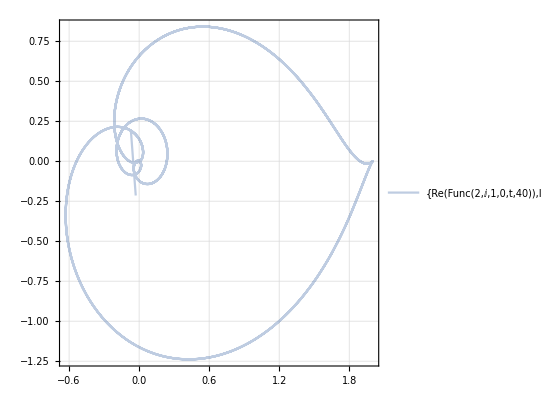

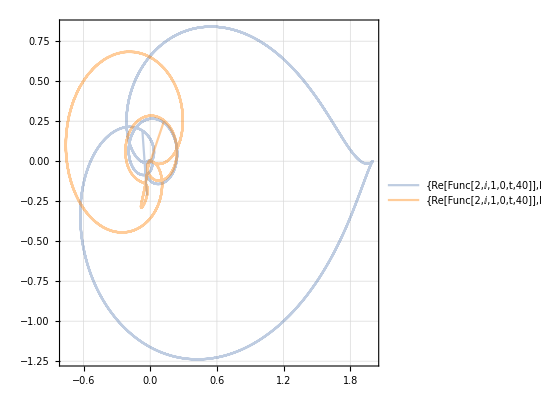

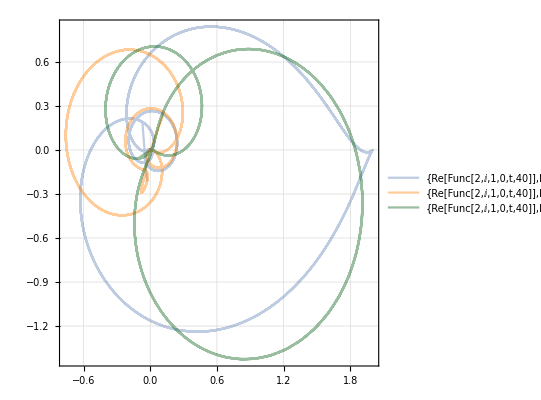

```mathematica
Show[p1]
Show[p1,p2]
Show[p1,p2,p3]
```

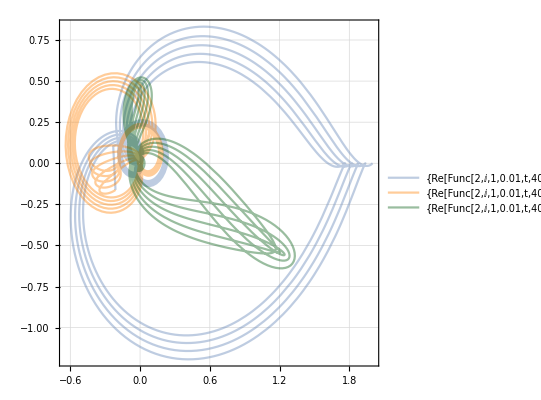

```mathematica
p11=ParametricPlot[{Re[Func[2,ⅈ,1,0.01,t,40]],Im[Func[2,ⅈ,1,0.01,t,40]]},{t,0,30},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],Thick}},AspectRatio->1];
p21=ParametricPlot[{Re[Func[2,ⅈ,1,0.01,t,40]],Im[Func[2,ⅈ,1,0.01,t,40]]},{t,30,60},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],Orange,Thick}},AspectRatio->1];
p31=ParametricPlot[{Re[Func[2,ⅈ,1,0.01,t,40]],Im[Func[2,ⅈ,1,0.01,t,40]]},{t,60,90},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],ColorData["AvocadoColors"][0.2],Thick},{Orange,Opacity[0.4]},{Gray}},AspectRatio->1];
Show[p11,p21,p31]
```

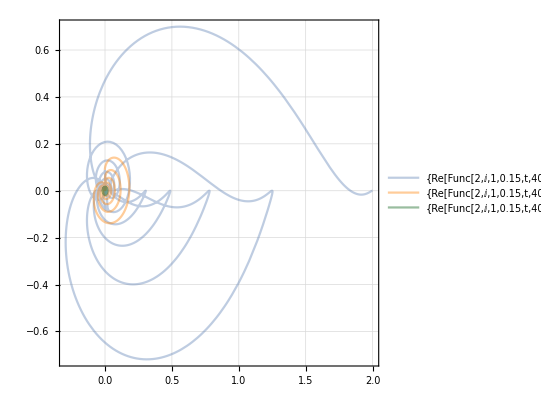

```mathematica
p11=ParametricPlot[{Re[Func[2,ⅈ,1,0.15,t,40]],Im[Func[2,ⅈ,1,0.15,t,40]]},{t,0,30},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],Thick}},AspectRatio->1];
p21=ParametricPlot[{Re[Func[2,ⅈ,1,0.15,t,40]],Im[Func[2,ⅈ,1,0.15,t,40]]},{t,30,60},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],Orange,Thick}},AspectRatio->1];
p31=ParametricPlot[{Re[Func[2,ⅈ,1,0.15,t,40]],Im[Func[2,ⅈ,1,0.15,t,40]]},{t,60,90},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{{Opacity[0.4],ColorData["AvocadoColors"][0.2],Thick},{Orange,Opacity[0.4]},{Gray}},AspectRatio->1];
Show[p11,p21,p31]
```

```mathematica
Ω[n_,β_,k_,t_]:=(β-k n +k (Efir[t]+ⅈ Efii[t]))ⅇ^(-ⅈ t)+k(n-Ef0[t])
Ωc[n_,β_,k_,t_]:=(β-k n +k (Efir[t]-ⅈ Efii[t]))ⅇ^(ⅈ t)+k(n-Ef0[t])
ComplexExpand[Ω[n+1,βr+ⅈ βi,k,t]*Ωc[n,βr-ⅈ βi,k,t]]
```

k^2 n+k^2 n^2-2 k^2 n Cos[t]-2 k^2 n^2 Cos[t]+k βr Cos[t]+2 k n βr Cos[t]+k^2 n Cos[t]^2+k^2 n^2 Cos[t]^2+βi^2 Cos[t]^2-k βr Cos[t]^2-2 k n βr Cos[t]^2+βr^2 Cos[t]^2-k^2 Ef0[t]-2 k^2 n Ef0[t]+k^2 Cos[t] Ef0[t]+2 k^2 n Cos[t] Ef0[t]-2 k βr Cos[t] Ef0[t]+k^2 Ef0[t]^2+2 k βi Cos[t]^2 Efii[t]+k^2 Cos[t]^2 Efii[t]^2+k^2 Cos[t] Efir[t]+2 k^2 n Cos[t] Efir[t]-k^2 Cos[t]^2 Efir[t]-2 k^2 n Cos[t]^2 Efir[t]+2 k βr Cos[t]^2 Efir[t]-2 k^2 Cos[t] Ef0[t] Efir[t]+k^2 Cos[t]^2 Efir[t]^2+k βi Sin[t]+2 k n βi Sin[t]-2 k βi Ef0[t] Sin[t]+k^2 Efii[t] Sin[t]+2 k^2 n Efii[t] Sin[t]-2 k^2 Ef0[t] Efii[t] Sin[t]+k^2 n Sin[t]^2+k^2 n^2 Sin[t]^2+βi^2 Sin[t]^2-k βr Sin[t]^2-2 k n βr Sin[t]^2+βr^2 Sin[t]^2+2 k βi Efii[t] Sin[t]^2+k^2 Efii[t]^2 Sin[t]^2-k^2 Efir[t] Sin[t]^2-2 k^2 n Efir[t] Sin[t]^2+2 k βr Efir[t] Sin[t]^2+k^2 Efir[t]^2 Sin[t]^2+ⅈ (-k βi Cos[t]+k βi Cos[t]^2-k^2 Cos[t] Efii[t]+k^2 Cos[t]^2 Efii[t]+k βr Sin[t]-k^2 Ef0[t] Sin[t]+k^2 Efir[t] Sin[t]+k βi Sin[t]^2+k^2 Efii[t] Sin[t]^2)

```mathematica
MonomialList[Simplify[-k βi Cos[t]+k βi Cos[t]^2-k^2 Cos[t] Efii[t]+k^2 Cos[t]^2 Efii[t]+k βr Sin[t]-k^2 Ef0[t] Sin[t]+k^2 Efir[t] Sin[t]+k βi Sin[t]^2+k^2 Efii[t] Sin[t]^2],k]
```

{k^2 (Efii[t]-Cos[t] Efii[t]-Ef0[t] Sin[t]+Efir[t] Sin[t]),k (βi-βi Cos[t]+βr Sin[t])}

```mathematica
∑_(n=0)^∞ (x^n*n)/(n!)
```

ⅇ^x x